## Automated process for creating graphical representation with the Wigner-D functions

```mathematica
ClearAll["Global`*"]
```

### Author: Robert Poenaru Date: 25th August 🗓

### Constant spin for a system

```mathematica
spin=3;
theta=π/3;
phi=π/6;
psi=π/2;
```

Create a set of projections M and K,  for a given spin I

```mathematica
wfComp[spin_]:=Table[{spin,m,k},{m,-spin,spin},{k,-spin,spin}];
```

Generate a set of Euler Angles using a pure function

```mathematica
angles[]={RandomReal[{π/6,π}],RandomReal[{π/6,π}],RandomReal[{π/6,π}]};
```

Create the first state φ_1=|I M=-I K=-I>
The state represents the lowest projections in the lab and intrinsic coordinate systems, respectively.
In the program, the state is denoted by `state1`

```mathematica
state1=wfComp[spin][[1]];
```

Create the list of all states φ_I=|I M_i K_i>
The group of all states φ_ij=|I M_i K_j> is called the stategroup

```mathematica
states[spin_]:=Table[wfComp[spin][[i]],{i,2*spin+1}];
stategroup=states[spin];
```

Print the states all the states φ_Mi for a given M

```mathematica
printer[states_,ith_]:=Do[Print[StringTemplate["φ_(`` ``)= "][ith-4,i-4],"|",states[[ith]][[i]]," >"],{i,1,2*spin+1}];
printer[stategroup,7]
```

φ_(3 -3)= |{3,3,-3} >

φ_(3 -2)= |{3,3,-2} >

φ_(3 -1)= |{3,3,-1} >

φ_(3 0)= |{3,3,0} >

φ_(3 1)= |{3,3,1} >

φ_(3 2)= |{3,3,2} >

φ_(3 3)= |{3,3,3} >

```mathematica
wigner[state_]:=Table[WignerD[state[[i]],angles[][[1]],angles[][[2]],angles[][[3]]],{i,1,2*spin+1}];
(*Create the real Wigner-D functions*)
rwd[state_]:=Table[Re[wigner[state][[i]]],{i,1,Length[wigner[state]]}];
```

Create plotting functions for Wigner-𝒟 functions

```mathematica
plotWD[state_]:=ListPlot[Labeled[#,#]&/@Table[Style[rwd[state][[i]],Black,13,Italic],{i,1,Length[wigner[state]]}],PlotRange->Full,Axes->False,Joined->True,Frame->True,PlotMarkers->{Automatic,11},PlotStyle->{Blue,Thick,Dashed},FrameLabel->{"φ_i|IMK>","𝒟_MK^I(ω)"},LabelStyle->{18,Bold,Black,FontFamily->"Times"},ImageSize->Large,FrameStyle->Directive[Black,Thick],AspectRatio->0.75,PlotRange->Automatic];
```

```mathematica
state1=stategroup[[1]]
state2=stategroup[[2]]
printer[stategroup,2]
```

{{3,-3,-3},{3,-3,-2},{3,-3,-1},{3,-3,0},{3,-3,1},{3,-3,2},{3,-3,3}}

{{3,-2,-3},{3,-2,-2},{3,-2,-1},{3,-2,0},{3,-2,1},{3,-2,2},{3,-2,3}}

φ_(-2 -3)= |{3,-2,-3} >

φ_(-2 -2)= |{3,-2,-2} >

φ_(-2 -1)= |{3,-2,-1} >

φ_(-2 0)= |{3,-2,0} >

φ_(-2 1)= |{3,-2,1} >

φ_(-2 2)= |{3,-2,2} >

φ_(-2 3)= |{3,-2,3} >

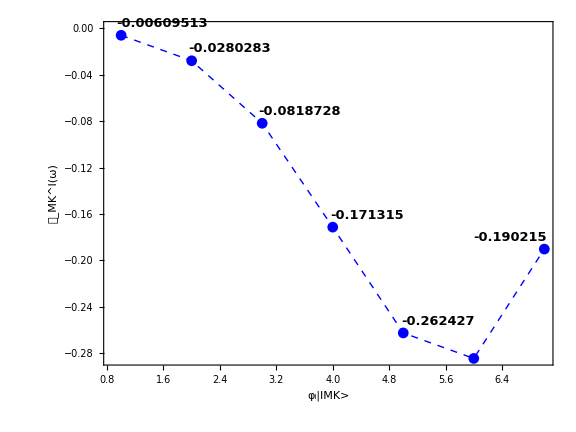

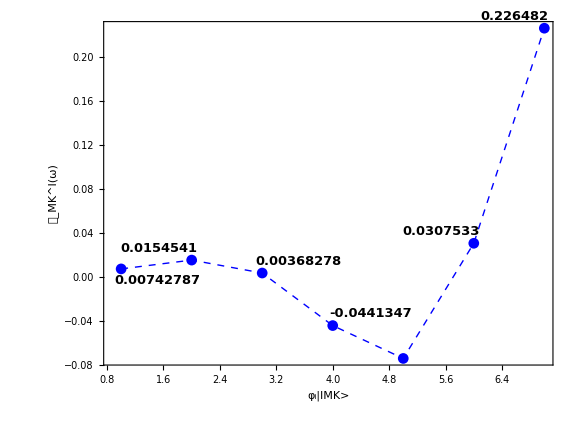

```mathematica
plotWD[state1]
plotWD[state2]
```